```mathematica
Gamma[0,s Log[n]]-Gamma[0,(s-1)Log[n]]+Log[s/(s-1)]
```

-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]+Log[s/(-1+s)]

```mathematica
Limit[-Gamma[0,2 Log[n]]+Gamma[0,3 Log[n]]+Log[3/2],n->Infinity]
```

Log[3/2]

```mathematica
D[Gamma[0,s Log[n]]-Gamma[0,(s-1)Log[n]]+Log[s/(s-1)],s]
```

n^(1-s)/(-1+s)-n^-s/s+((-1+s) (1/(-1+s)-s/(-1+s)^2))/s

```mathematica
Limit[n^(1-s)/(-1+s)-n^-s/s+((-1+s) (1/(-1+s)-s/(-1+s)^2))/s/.s->-1,n->Infinity]
```

-∞

```mathematica
Limit[Log[(1-2^(1-s))Zeta[s]],s->1]
```

Log[Log[2]]

```mathematica
Limit[Log[(1-2^(1-s))]+Log[Zeta[s]],s->1]
```

Log[Log[2]]

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!

Clear[kappa2,pk]
kappa2[n_]:=kappa2[n]=If[ MangoldtLambda[n]/Log[n] == 0, 0, FullSimplify[MangoldtLambda[n]/Log[n]] (-1)^(1/(FullSimplify[MangoldtLambda[n]/Log[n]]))]
pk[n_,0]:=1
pk[n_,k_]:=pk[n,k]=Sum[kappa2[j] pk[Floor[n/j],k-1],{j,2,n}]
Dnz12[n_,z_]:=Sum[z^k/k! pk[n,k],{k,0,Log[2,n]}]

FI[n_]:=FactorInteger[n]
FI[1]:={}
Dnz13[n_,s_,z_]:=Sum[j^-s Product[ binomial[-z,p[[2]]],{p,FI[j]}],{j,1,n}]
```

```mathematica
N[Table[FullSimplify[D[-Dnz13[n,s,1],s]/.s->0],{n,90,100}]]
```

{-11.1004,-6.58952,-11.1113,-6.57871,-2.03542,2.51846,7.08281,2.5081,-2.07687,-6.67199,-2.06682}

```mathematica
Sum[ N[ LiouvilleLambda[j] Log[j]],{j,2,100}]
```

-2.06682

```mathematica
N[D[D[Dnz13[10000,s,z],z]/.z->0,s]/.s->2]
```

0.442522

```mathematica
N[Log[(Zeta[4]/Zeta[2])]]
```

-0.41859

```mathematica
Expand[D[Zeta[2s]/Zeta[s],s]/(Zeta[2s]/Zeta[s])]
```

-Zeta'[s]/Zeta[s]+(2 Zeta'[2 s])/Zeta[2 s]

```mathematica
N[-Zeta'[s]/Zeta[s]+(2 Zeta'[2 s])/Zeta[2 s]/.s->2]
```

0.442621

```mathematica
FI[n_]:=FactorInteger[n]
FI[1]:={}
Dnz13[n_,s_,z_]:=Sum[j^-s Product[ binomial[-z,p[[2]]],{p,FI[j]}],{j,1,n}]
Dnz13o[n_,s_,z_]:=Sum[j^-s Product[(-1)^p[[2]] binomial[-z,p[[2]]],{p,FI[j]}],{j,1,n}]
pp[n_,s_, z_] := Sum[ (Dnz13o[j,s,-z]-Dnz13o[j-1,s,-z])Dnz13o[Floor[(n/j)^(1/2)],2 s, z],{j,1,n}]
pp2[n_,s_, z_] := Sum[ (Dnz13o[j,2 s,z]-Dnz13o[j-1,2 s,z])Dnz13o[n/j^2, s, -z],{j,1,n^(1/2)}]
oo[n_,s_, z_] := Sum[ (Dnz13[j,s,-z]-Dnz13[j-1,s,-z])Dnz13[Floor[(n/j)^(1/2)],2 s, z],{j,1,n}]
oo2[n_,s_, z_] := Sum[ (Dnz13[j, s,-z]-Dnz13[j-1, s,-z])Dnz13[n/j^2, 2s, z],{j,1,n^(1/2)}]
oo3[n_] := Sum[MoebiusMu[j]Dnz13[n/j^2, 0, 1],{j,1,n^(1/2)}]
oo3a[n_,s_, z_] := Sum[ (Dnz13o[j, s,-z]-Dnz13o[j-1, s,-z])Dnz13[n/j^2, 2s, z],{j,1,n^(1/2)}]
(* irk *)
oo4a[n_,s_, z_] := Sum[ (Dnz13[k^2, s,-z]-Dnz13[k^2-1, s,-z])Dnz13[n/j^2, 2s, -z],{j,1,n^(1/2)},{k,1,n^(1/2)}]
pp2a[n_] := Sum[D[(Dnz13o[j,0,z]-Dnz13o[j-1,0,z])Dnz13o[n/j^2, 0, -z],z]/.z->0,{j,1,n^(1/2)}]
pp2a[n_,s_, z_] := Sum[( Dnz13o[Floor[j^(1/2)], s,-z]-Dnz13o[Floor[(j-1)^(1/2)], s,-z])Dnz13o[n/j, 2s, z],{j,1,n}]
oo2a[n_,s_, z_] := Sum[( Dnz13[Floor[j^(1/2)], s,-z]-Dnz13[Floor[(j-1)^(1/2)], s,-z])Dnz13[n/j, 2s, z],{j,1,n}]
pp2b[n_,s_, z_] := Sum[( Dnz13o[Floor[j^(1/2)], s,-z]-Dnz13o[Floor[(j-1)^(1/2)], s,-z])Dnz13o[n/j, 2s, z],{j,1,n}]
```

```mathematica
Expand[oo2a[100,0,z]]
```

1-(298 z)/15+(5549 z^2)/360-(85 z^3)/48+(299 z^4)/144+(11 z^5)/80+(7 z^6)/720

```mathematica
Expand[pp2a[100]]
```

-116/5

```mathematica
Expand[oo2a[100,0,z]]
```

1-(298 z)/15+(5549 z^2)/360-(85 z^3)/48+(299 z^4)/144+(11 z^5)/80+(7 z^6)/720

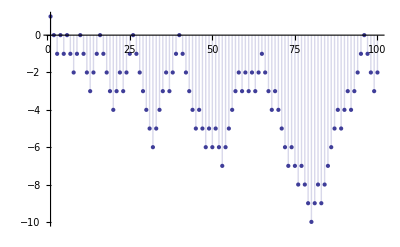

```mathematica
DiscretePlot[ pp[n,0,1],{n,1,100}]
```

```mathematica
pp2b[n_,s_, z_] := Sum[( Dnz13o[Floor[j^(1/4)], s,-z]-Dnz13o[Floor[(j-1)^(1/4)], s,-z])Dnz13o[n/j, 4s, z],{j,1,n}]
Table[{n,D[(pp2b[2^n,0,z]-pp2b[2^n-1,0,z]),z]/.z->0},{n,1,10}]//TableForm
```

1 | 1
2 | 1/2
3 | 1/3
4 | -3/4
5 | 1/5
6 | 1/6
7 | 1/7
8 | -3/8
9 | 1/9
10 | 1/10

```mathematica
K[n_] := K[n]=If[ n ≠ Floor[n],0,FullSimplify[ MangoldtLambda[ n] / Log[n]]]
kl[n_] := K[n] -  K[n^(1/2)]
```

```mathematica
Table[kl[n],{n,2,33}]
```

{1,1,-1/2,1,0,1,1/3,-1/2,0,1,0,1,0,0,-1/4,1,0,1,0,0,0,1,0,-1/2,0,1/3,0,1,0,1,1/5,0}

```mathematica
K[16]
```

1/4

```mathematica
Clear[dd,jord]
FI[n_]:=FactorInteger[n]
FI[0]:={}
FI[1]:={}
dd[n_,s_,z_]:=dd[n,s,z]=Sum[j^-s Product[(-1)^p[[2]] binomial[-z,p[[2]]],{p,FI[j]}],{j,1,n}]
dd[0,s_,z_]:=0
jord[n_,k_]:=jord[n,k]=n^k Product[1-1/p[[1]]^k,{p,FI[n]}]
js[n_,s_,k_] := Sum[ j^-s jord[j,k],{j,1,n}]
sig[n_,s_,k_] := Sum[ j^-s DivisorSigma[k,j],{j,1,n}]
tot[n_,s_,k_] := Sum[ j^-s jord[j,k],{j,1,n}]
tot2[n_,s_,k_] := Sum[ (dd[j,s-k,1]-dd[j-1,s-k,1])dd[n/j,s,-1],{j,1,n}]
dsigma[n_,s_,k_] := Sum[ (dd[j,s-k,1]-dd[j-1,s-k,1])dd[n/j,s,1],{j,1,n}]
ds2[n_, s_, a_, k_] := Sum[ j^-s DivisorSigma[a,j] ds2[n/j, s,a,k-1],{j,2,n}]
ds2[n_,s_,a_,0]:=1
dsz[n_, s_, a_, z_] := Sum[ Binomial[ z,k]ds2[n,s,a,k],{k,0,Log[2,n]}]
dsigmaz[n_,s_,a_,z_] := Sum[ (dd[j,s-a,z]-dd[j-1,s-a,z])dd[n/j,s,z],{j,1,n}]
```

```mathematica
tot2[100,-2,2]
```

1696967413

```mathematica
js[100,-2,2]
```

1696967413

```mathematica
dsigma[100,-1,2]
```

30766703

```mathematica
sig[100,-1,2]
```

30766703

```mathematica
dsz[100,-1,-2,-3]
```

2682015571623969862865333635975968635064127/363126954321419151898613588204751581025

```mathematica
dsigmaz[100,-1,-2,-3]
```

2682015571623969862865333635975968635064127/363126954321419151898613588204751581025

```mathematica
rr[n_] := Sum[ DivisorSigma[0,j^2],{j,1,n}]
```

```mathematica
rr[100]
```

1194

```mathematica
Sum[ (dd[j^2,0,3]-dd[j^2-1,0,3])dd[Floor[100/j^2],0,-1],{j,1,10}]
```

35

```mathematica
px[n_,s_, z_] := Sum[( dd[Floor[j^(1/2)], s,3 z]-dd[Floor[(j-1)^(1/2)], s,3 z])dd[n/j, 2s, -z],{j,1,n}]
```

```mathematica
px[100,0,1]
```

5

```mathematica
Clear[K]
K[n_] :=If[n<2,0, FullSimplify[ MangoldtLambda[ Floor[n]] / Log[Floor[n]]]]
k2[n_] := K[n]-(K[n^(1/2)]-K[(n-1)^(1/2)])
```

```mathematica
Table[ k2[n],{n,1,20}]
```

{0,1,1,-1/2,1,0,1,1/3,1/2,0,1,0,1,0,0,3/4,1,0,1,0}

```mathematica
D[Log[Zeta[s+a]]-Log[Zeta[s]],s]
```

-Zeta'[s]/Zeta[s]+Zeta'[a+s]/Zeta[a+s]